```mathematica
ClearAll["Global`*"]
```

# Plotting for K-Nearest Neighbors

This script generates the plot of errors for the K-nearest neighbors algorithm for K = 1, ..., 25

## Input Data

The list of errors to plot.

```mathematica
errors={0.3132514893243485,0.2810638905864732,0.26756866584674094,0.2605038021985107,0.25571528411190514,0.2552946739156313,0.25193242916879177,0.2504314567798961, 0.25311324297106425,0.2516530059173058,0.2509167947077423, 0.24915287876035402,0.25086055649968075,0.2502668770734082,0.24997019453637911,0.2504174870194971,0.25017797666998576, 0.25067298600944277,0.25115301560411385,0.2503263013207967, 0.251138668922084,0.25186802835311684,0.2508385558335431,0.2508842143383406,0.2521475849831992}
```

{0.313251,0.281064,0.267569,0.260504,0.255715,0.255295,0.251932,0.250431,0.253113,0.251653,0.250917,0.249153,0.250861,0.250267,0.24997,0.250417,0.250178,0.250673,0.251153,0.250326,0.251139,0.251868,0.250839,0.250884,0.252148}

## Plot Generation

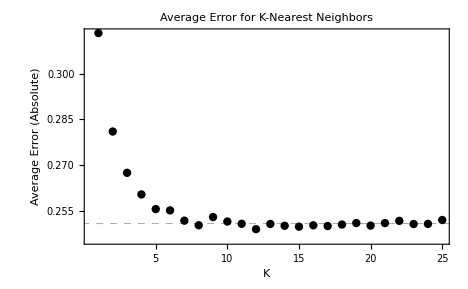

```mathematica
ListPlot[errors,
PlotRange->All,
Axes->False,
Frame->{{True,False},{True,False}},
GridLines->{{},{Mean[errors[[7;;]]]}},
PlotLabel->"Average Error for K-Nearest Neighbors",
FrameLabel->{{"Average Error (Absolute)",},{"K",}},
PlotStyle->Directive[Black,Dashed,Thick],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,FontSize->16,FontFamily->"Times"],
GridLinesStyle->Directive[Gray,Thick,Dashed],
ImageSize->(72*6.5)
]
```

```mathematica
Mean[errors[[7;;]]]
```

0.250943